# Calculations supporting Patterns of entropy creation in gravitational collapse, Wren (2018)

This notebook provides calculations supporting this paper, prepared for submission to MNRAS.

It is structured in line with the Appendices to Wren (2018), which cite this notebook.  All the paper’s Figures, including those in the main text, are also generated by this notebook.

All equation and other references are to Patterns of entropy creation in gravitational collapse, Andrew J Wren (2018).

There is a supporting data file for this notebook, “Patterns Wren 2018 data.m” which should be downloaded, and placed in the directory from which your Mathematica reads files.  The relevant parts of this notebook also provide (commented out) the code which generated this file.

Respond “Yes” when, on evaluation, the notebook asks to automatically evaluate all initialisation cells. 

The notebook takes around 10-20 minutes to run on a standard PC.

We assume throughout that,

```mathematica
$Assumptions=Subscript[k, J]>0&&σ>0&&V>0&&σ1>0&&κ>0&&-1≤cth≤1&&1≤cpsi≤1;
```

k_J, σ, V, and σ1 are defined in the paper.  A dummy variable κ is frequently used in order to help derive power series up to a given order in a set of k variables.  Every  k_1, k_2 or k_+ is paired with a κ, so, for example the magnitude k_1^2 becomes (κ k_1)^2.  Series are then expanded up to a power of κ, which is the easiest way to expand up to a given total power of any product of k_1, k_2 and k_+.  At the end of our calculations, κ is set to 1. cth and cpsi are defined in the part of this notebook relating to Appendix F.

## Appendices B1 and B2

## Calculations for equations in Appendices B1 and B2

The next lines are the formula for approximating Z given in Eq. (B2), including its expansion to four terms, both only for Im[z]>0:

```mathematica
Zapprox[z_,numberofZterms_]:=-Sum[((j-1/2)!)/(√π*z^(2*j+1)),{j,0,numberofZterms-1}]
```

```mathematica
Zapprox[z,4]
```

-15/(8 z^7)-3/(4 z^5)-1/(2 z^3)-1/z

This implies, via Eq. (37) the following formula for P(k,ω), again only for Im[z]>0:

```mathematica
Papprox[k_,ω_,numberofPterms_]:=1+ω/(√2*σ*k)*Zapprox[ω/(√2*σ*k),numberofPterms+1]
```

```mathematica
Expand[Papprox[k,ω,4]]
```

-(105 k^8 σ^8)/ω^8-(15 k^6 σ^6)/ω^6-(3 k^4 σ^4)/ω^4-(k^2 σ^2)/ω^2

Now check the formula for the zero of the dispersion relation k^2=k_J^2 P(k,ⅈη), as given in Eq. (B4),

```mathematica
η=Subscript[k, J] σ-(3σ k^2)/(2 Subscript[k, J])+(15σ k^4)/(8 Subscript[k, J]^3)-(147σ k^6)/(16 Subscript[k, J]^5)+(9531σ k^8)/(128 Subscript[k, J]^7);
```

Confirm that this formula for η satisfies the dispersion relation up to and including order 9 in k:

```mathematica
Series[k^2-Subscript[k, J]^2 Papprox[k,ⅈ*η,4],{k,0,9}]
```

O[k]^10

## Calculation of Figure 1

This uses the method described in the paragraph containing Eq. (B5), which is expressed in the next function.  Here, and for other figures, we have chosen units so that σ=k_J=1

```mathematica
Z[z_]:=Which[Im[z]≥1,ContinuedFractionK[If[n==1,z,-1/2 (-1+n) (-3+2 n)],-z^2-3/2+2 n,{n,1,20}],-1<Im[z]<1,ⅈ*√π*Exp[-z^2]*(1+Erf[ⅈ*z]),Im[z]≤-1,2*ⅈ*√π*Exp[-z^2]+Conjugate[ContinuedFractionK[If[n==1,Conjugate[z],-1/2 (-1+n) (-3+2 n)],-Conjugate[z]^2-3/2+2 n,{n,1,20}]],True,"Error"]
```

```mathematica
P[k_,ω_]:=1+ω/(√2*k)*Z[ω/(√2*k)]
```

Numerically find a zero for the dispersion equation:

```mathematica
positiveimaginarydispersionzero[k_]:=Im[FindRoot[P[k,ω]==k^2,{ω,ⅈ}][[1,2]]]
```

Produce Figure 1:

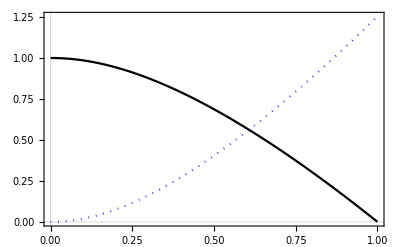

```mathematica
Figure1=Plot[{positiveimaginarydispersionzero[k],(1-k^2-positiveimaginarydispersionzero[k]^2)/positiveimaginarydispersionzero[k]},{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],""},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->{Black,{Blue,Dotted}},PlotPoints->1000,PlotLegends->{MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->1.25*1.3],MaTeX["\\frac{\\sigma^2\\left(k_\\text{J}^2-k^2\\right)-\\eta(k)^2}{k_\\text{J}\\eta(k)\\sigma}",Magnification->0.9*1.3]}]
```

If uncommented, export Figure 1 as a pdf file:

```mathematica
(*Export["EGCFigure1.pdf",Figure1];*)
```

## Calculation of Figure B1

Calculate the left plot of Figure B1, using the previous two sections of this notebook:

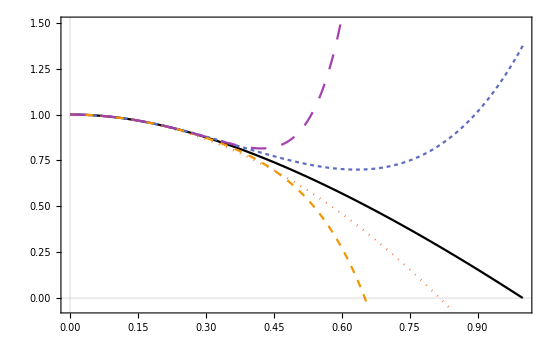

```mathematica
FigureB1left=Plot[{positiveimaginarydispersionzero[k],1-3/2 k^2,1-3/2 k^2+15/8 k^4,1-3/2 k^2+15/8 k^4-147/16 k^6,1-3/2 k^2+15/8 k^4-147/16 k^6+9531/128 k^8},{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->2],MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->2]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8,PlotPoints->1000,ImageSize->554,PlotRange->{Full,{-0.05,1.5}},ImagePadding->{{Automatic,Automatic},{Automatic,None}}]
```

The following (which takes some time to evaluate) calculates the right plot of Figure B1, again using the previous two sections of this notebook:

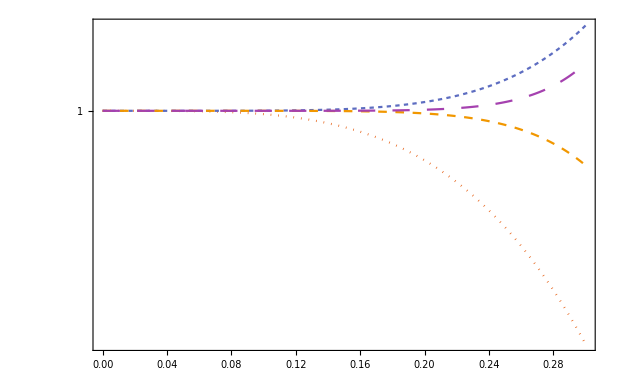

```mathematica
FigureB1right=LogPlot[{(1-3/2 k^2)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4-147/16 k^6)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4-147/16 k^6+9531/128 k^8)/positiveimaginarydispersionzero[k]},{k,0,0.3},FrameLabel->{MaTeX["\\quad\\sfrac{k}{k_\\text{J}}",Magnification->2],MaTeX["\\sfrac{\\text{Series}}{\\text{Exact}}",Magnification->2]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8log,PlotPoints->1000,ImageSize->620,GridLines->{{0},{1-1 10^-2,1-1 10^-3,1,1+1 10^-3}},PlotRange->Full,FrameTicks->laxsticks,ImagePadding->{{Automatic,Automatic},{Automatic,None}}]
```

Combine the above to make the full figure:

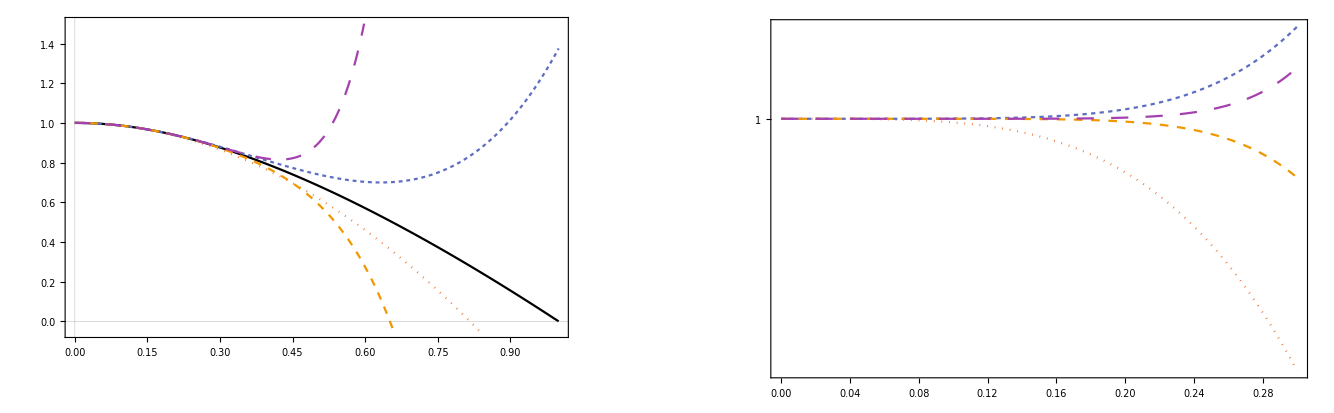

```mathematica
FigureB1=Legended[GraphicsRow[{FigureB1left,FigureB1right},Alignment->Top],Placed[LineLegend[ps8,pl,LegendLayout->"Row"],Below]]
```

If uncommented, export Figure B1 as a pdf file :

```mathematica
(*Export["EGCFigureB1.pdf",FigureB1];*)
```

## Appendix B3

This section of the notebook does the calculations referred to in the paragraph following that of Eq. (B11), checking the formula for the size and argument of the dispersion zeros given in Eqs. (B10) and (B11) respectively

Define a function which numerically finds dispersion relation zeros with negative imaginary parts:

```mathematica
negativeimaginarydispersionzero[k_,start_]:=FindRoot[P[k,ω]==k^2,{ω,start*(1-ⅈ)/(√2)}][[1,2]]
```

Using this, define a function which generates a set of such zeros, using a range of start points for the numerical calculation.  (The function only admits solutions which satisfy the dispersion relation sufficiently accurately, and suppresses error messages which will be associated with rejected solutions.  It also rounds solutions to decimalplaces decimal places, and de-duplicates.)

```mathematica
setofzeros[k_,begintstartrange_,endstartrange_,decimalplaces_]:=Quiet[SortBy[DeleteDuplicatesBy[Cases[Table[If[Abs[P[k,result=negativeimaginarydispersionzero[k,start]]-k^2]<=10^-decimalplaces,Chop[result]],{start,begintstartrange,endstartrange,10^-decimalplaces}],Except[Null]],(Round[#,10^-decimalplaces])&],Re]]
```

Uncommented, the next line was originally used (taking an hour or two on a standard PC) to calculate (and export) zeros ω in the range 10< |ω|<11 for k=0.1 k_J and k=0.01 k_J...

```mathematica
(*B3data1=Cases[setofzeros[0.1,9,12,4],ω_/;10<Abs[ω]<11];B3data2=Cases[setofzeros[0.01,9,12,5],ω_/;10<Abs[ω]<11];B3data={B3data1,B3data2};Export["Appendix B3 data.m",B3data];*)
```

...but it can also be more quickly imported from a data file comprising this and other data, using the next line

```mathematica
B3data=<<"Patterns Wren 2018 data.m"[[1]];
```

From the numerical solutions for the dispersion relation, count the number of zeros ω in the range 10< |ω|<11, for, respectively, k=0.1 k_J and k=0.01 k_J:

```mathematica
Map[Length,B3data]
```

{168,16712}

Define a function counting the number of zeros according to the approximation in Eq. (B10):

```mathematica
nozerosEqB10[k_,ω1_,ω2_]:=(Ceiling[(k^2 π+2 Max[ω1,ω2]^2)/(8 k^2 π)]-1)-(Floor[(k^2 π+2 Min[ω1,ω2]^2)/(8 k^2 π)]+1)+1
```

Count the number of zeros predicted by Eq. (B10) for, respectively, k=0.1 k_J and k=0.01 k_J:

```mathematica
nozerosEqB10[{0.1,0.01},10,11]
```

{168,16711}

Calculate the maximum deviation from the diagonal from the numerical solutions for the dispersion zeros:

```mathematica
(paddedscientificform[(Arg[MaximalBy[#,Arg]][[1]]-(-π/4)),3])&/@B3data
```

{ 1.01×10^-3, 1.70×10^-5}

To calculate the maximum deviation from the diagonal using the approximation in Eq. (B11), first find the index number n for the first zero ω in the range 10< |ω|<11:

```mathematica
nfirstzero=(Floor[(#^2 π+2*10^2)/(8 #^2 π)]+1)&/@{0.1,0.01};
```

Then calculate the deviation from the diagonal for those n, as predicted by Eq. (B11):

```mathematica
deviationB11[k_,n_]:=1/(4 π (n-1/8)) Log[(π √(2(n-1/8)))/k^2]
```

```mathematica
paddedscientificform[{deviationB11[0.1,nfirstzero[[1]]],deviationB11[0.01,nfirstzero[[2]]]},3]
```

{ 9.44×10^-4, 1.63×10^-5}

## Appendix E

This part calculates a series expansion for I_D_1, see Eq. (E26), for use in Eq. (E28), and from that then derives Eq. (E29) for γ_a(k_1,v_1,k_2,t).

Aside, which may safely be ignored: We do all power series expansions initially to order 8 to be sure that no terms are missed, in particular in calculating I_D_1, which as a sum of terms might see cancellations which increase its leading order.  In fact, this does not occur and the leading order of I_D_1 is zero.  It can be seen from adjusting this this notebook that calculating all expressions initially to order 4 (but no less) would be sufficient.

## Quantities that occur in Eq. (E26)

Ensure we do not define η_1, η_2 and ηE=η_1+η_1 until later:

```mathematica
Clear[η1];Clear[η2];Clear[ηE];
```

Y(k_1,ⅈ η_1) and Y(k_2,ⅈ η_2) are written using the dispersion relation:

```mathematica
Y11=((κ k1)^2-Subscript[k, J]^2)/(Subscript[k, J]^2 ⅈ η1);Y22=((κ k2)^2-Subscript[k, J]^2)/(Subscript[k, J]^2 ⅈ η2);
```

From these, we get P(k_1,ⅈ η_1) and P(k_2,ⅈ η_2):

```mathematica
P11=1+ⅈ η1 Y11;P22=1+ⅈ η2 Y22;
```

Also define expressions for the derivative of the Y and P functions with respect to the ω variables, which can be found using the expression mentioned after Eq. (B17),

```mathematica
dY11=-1/(κ k1 σ)^2 (1+ⅈ η1 Y11);dY22=-1/(κ k2 σ)^2 (1+ⅈ η2 Y22);dP11=Y11+ⅈ η1 dY11;dP22=Y22+ⅈ η2 dY22;
```

Derive a series expansion for the function Y(k,ω,k_+,ω_+) from Eq. (E23), writing kppa and kppe for the parts of k_+ respectively parallel and perpendicular to k, and ωp for ω_+.  The easiest way to do this is to use Mathematica’s Expectation function to evaluate the Gaussian “moments”, using an approach similar to that which derives the series for Eq. (B2).

```mathematica
Ydouble=Collect[Expand[Expectation[Normal[Series[1/((κ k) vpa-ω) 1/((κ kppa) vpa+(κ kppe) vpe-ωp),{κ,0,8}]],{vpa,vpe}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]]],{κ}];
```

We will also need its derivative with respect to ω:

```mathematica
dYdouble=D[Ydouble,ω];
```

Write Y(k_1,ⅈ η_1,k_+,ⅈ E) and Y(k_2,ⅈ η_2,k_+,ⅈ E), and also related derivatives:

```mathematica
Y11pE=Simplify[Ydouble//.{k->k1,ω->ⅈ η1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
Y22pE=Simplify[Ydouble//.{k->k2,ω->ⅈ η2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
dY11pE=Simplify[dYdouble//.{k->k1,ω->ⅈ η1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
dY22pE=Simplify[dYdouble//.{k->k2,ω->ⅈ η2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

Write P(k_1,ⅈ η_1,k_+,ⅈ E) and P(k_2,ⅈ η_2,k_+,ⅈ E), and related derivatives, using Eq. (E24):

```mathematica
P11pE=Y11+ⅈ ηE Y11pE;P22pE=Y22+ⅈ ηE Y22pE;dP11pE=dY11+ⅈ ηE dY11pE;dP22pE=dY22+ⅈ ηE dY22pE;
```

We also need Y(k_+,ⅈ E) and P(k_+,ⅈ E):

```mathematica
YpE=Simplify[Normal[Series[-1/(ⅈ ηE)-(σ^2 (κ kp)^2)/(ⅈ ηE)^3-(3 σ^4 (κ kp)^4)/(ⅈ ηE)^5-(15 σ^6 (κ kp)^6)/(ⅈ ηE)^7-(105 σ^8 (κ kp)^8)/(ⅈ ηE)^9,{κ,0,8}]]];PpE=1+ⅈ ηE YpE;
```

We now define expressions for η_1, η_2 and ηE.  Had we done so earlier, some of the above evaluations would have been much slower.  Use Eq. (A4) to define η_1 and η_2:

```mathematica
η1=Subscript[k, J] σ-(3 σ (κ k1)^2)/(2 Subscript[k, J])+(15 σ (κ k1)^4)/(8 Subscript[k, J]^3)-(147 σ (κ k1)^6)/(16 Subscript[k, J]^5)+(9531 σ (κ k1)^8)/(128 Subscript[k, J]^7);η2=Subscript[k, J] σ-(3 σ (κ k2)^2)/(2 Subscript[k, J])+(15 σ (κ k2)^4)/(8 Subscript[k, J]^3)-(147 σ (κ k2)^6)/(16 Subscript[k, J]^5)+(9531 σ (κ k2)^8)/(128 Subscript[k, J]^7);ηE=η1+η2;
```

We also define expressions for q̄(k_1) and q̄(k_2),

```mathematica
q1=-Subscript[k, J]^2/(V (Subscript[k, J]^2-(κ k1)^2));q2=-Subscript[k, J]^2/(V (Subscript[k, J]^2-(κ k2)^2));
```

## Evaluating Eqs. (E26) and (E28) to get Eq. (E29)

This then enables us to write a series expansion for Eq. (E26) as

```mathematica
ID1=Normal[Series[(((Subscript[k, J]^2 P11)/(κ k1)^2 (Y22pE+(Subscript[k, J]^2 P22pE YpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k1dotkp P11 Y22 YpE)/((κ k1)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q2+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y22)/(κ k2)^2 (dY11pE+(Subscript[k, J]^2 YpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP11pE) (V q2+1))+((Subscript[k, J]^2 P22)/(κ k2)^2 (Y11pE+(Subscript[k, J]^2 P11pE YpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k2dotkp P22 Y11 YpE)/((κ k2)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q1+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y11)/(κ k1)^2 (dY22pE+(Subscript[k, J]^2 YpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP22pE) (V q1+1))),{κ,0,8}]];
```

The remaining factors in Eq. (E28), other than the Maxwellian and the time exponential, can be written as

```mathematica
E28remaining=Simplify[-((κ k1dotv1)/(κ k1dotv1-ⅈ η1) ((Subscript[k, J]^2 η1 η2 σ^4 (κ k2)^2)/((σ^2 (Subscript[k, J]^2-(κ k1)^2)-η1^2) (σ^2 (Subscript[k, J]^2-(κ k2)^2)-η2^2))))];
```

where k1dotv1 is k_1·v_1.  The right-hand side of Eq. (E29), other than the Maxwellian and the time exponential, can therefore be written as the following:

```mathematica
E29expression=Collect[Series[E28remaining ID1,{κ,0,2}]//.{k2dotkp->kp^2-k1dotkp,k1dotk2->k1dotkp-k1^2,k2^2->kp^2+k1^2-2 k1dotkp},{κ,k1dotv1 },Simplify];
```

Set the dummy variable κ to 1 to get the final expression:

```mathematica
E29expressionNoκ=E29expression/.{κ->1}
```

k1dotv1^2/(4 k1^2 σ^2)-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4))/(12 k1^2 kp^2 σ^2 k_J^2)-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4))/(24 k1^2 kp^2 σ k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 σ)

The above expression is the factor on the right-hand side of  Eq. (E29), in braces, which when multiplied by the Maxwellian and the time exponential, as set out in that equation, gives γ_a(k_1,v_1,k_2,t).

We will also need it in its form with κ to use for Appendix F,

```mathematica
E29expression
```

k1dotv1^2/(4 k1^2 σ^2)+κ^2 (-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4))/(12 k1^2 kp^2 σ^2 k_J^2))+κ (-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4))/(24 k1^2 kp^2 σ k_J))+(ⅈ k1dotv1 k_J)/(4 k1^2 κ σ)

## Appendix F

## Calculating the driving matrix (D̃)_1

From Eq. (E3), neglecting terms of higher order in V^-1, and leaving aside Maxwellian factors, we have

```mathematica
D1tilde[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2 kp.v1)/(kp.kp) intf1[kp] V q[k2]+(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df1[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f1[kp,v2]+(ⅈ Subscript[k, J]^2 kp.v2)/(kp.kp) intf1[kp] V q[k1]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df1[kp,v2] (V q[k1]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f1[kp,v1]
```

where f1, intf1, and df1 are, respectively, the function OverTilde[f^-]_1, and its integral and derivative with respect to velocity, all implicitly curtailed at some suitable power in k.  From Eqs. (39) and (B2), we have, leaving aside the Maxwellian factor, a series expansion

```mathematica
f1[p_,v_]:=ⅈ/ω (1+(p.v)/ω+((p.v)/ω)^2+((p.v)/ω)^3+((p.v)/ω)^4)-((ⅈ Subscript[k, J]^2 p.v (ω^2+p.p σ^2+(3 σ^4 (p.p)^2)/ω^2+(15 σ^6 (p.p)^3)/ω^4))/(ω^2 p.p (ω^2+Subscript[k, J]^2 σ^2+(3 Subscript[k, J]^2 σ^4 (p.p))/ω^2+(15 Subscript[k, J]^2 σ^6 (p.p)^2)/ω^4))) (1+(p.v)/ω+((p.v)/ω)^2+((p.v)/ω)^3+((p.v)/ω)^4+((p.v)/ω)^5+((p.v)/ω)^6)
```

Note that use of p as the momentum variable is to avoid a variable k and the constant k_J getting confused by Mathematica. For the same reason k must not be used as a variable to which f1 is applied, although, for example k1 and k2, as in the definition of D1tilde do not cause any such problems.

Similarly, we have the integral of f1 with respect to v is

```mathematica
intf1[p_]:=ⅈ (1/ω+(σ^2 p.p)/ω^3+(3 σ^4 (p.p)^2)/ω^5)-(ⅈ (ω^2+σ^2 p.p) (σ^2+(3 σ^4 p.p)/ω^2) Subscript[k, J]^2)/(ω^3 (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2))
```

and the derivative of f1 with respect to v is

```mathematica
df1[p_,v_]:=(ⅈ p (1/ω+(2 p.v)/ω^2+(3 (p.v)^2)/ω^3))/ω-(ⅈ v (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3))/(σ^2 ω)-(ⅈ (ω^2+σ^2 p.p+(3 σ^4 (p.p)^2)/ω^2) p.v (p/ω+(2 p p.v)/ω^2+(3 p (p.v)^2)/ω^3+(4 p (p.v)^3)/ω^4) Subscript[k, J]^2)/(ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))-(ⅈ p (ω^2+σ^2 p.p+(3 σ^4 (p.p)^2)/ω^2) (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3+(p.v)^4/ω^4) Subscript[k, J]^2)/(ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))+(ⅈ v (ω^2+σ^2 p.p+(3 σ^4 (p.p)^2)/ω^2) p.v (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3+(p.v)^4/ω^4) Subscript[k, J]^2)/(σ^2 ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))
```

while, from Eq. (43), we have, neglecting terms of higher order in V^-1, a series expansion up to order p^4,

```mathematica
q[p_]:=-1/V-(p.p)/(Subscript[k, J]^2 V)-(p.p)^2/(Subscript[k, J]^4 V)
```

which gives us all the functions making up D1tilde.

## Calculating the vector ν (nu)

From the definition of ν^(j)(k_1,k_2) in Eq. (F4), we need a factor,

```mathematica
F4factor[k1_,v1_,k2_,v2_]:=1+(k1.v1+k2.v2)/ω+((k1.v1+k2.v2)/ω)^2+((k1.v1+k2.v2)/ω)^3+((k1.v1+k2.v2)/ω)^4
```

Eq. (F10) defines  the vector ν (nu). Its first component is μ^(0) which is 0.  The second, fourth and sixth components are given by ν^(j)(k_1,k_2) for j=1,2,3.  The third, fifth and seventh are similarly ν^(j)(k_2,k_1).We write k_1 and k_2 in co-ordinate terms with their moduli k1 and k2, and the angle θ, which  k_2 makes to k_1; and we also now introduce the dummy variable κ.  Calculating ν takes less than two minutes on a standard PC:

```mathematica
ν=Join[{0},Flatten[Table[{term=Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] F4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},σ^2 IdentityMatrix[4]]],{κ,0,3}]],term/.{k1->k2,k2->k1,θ->-θ}},{j,1,3}]]];
```

## Constructing the matrix M

We construct M row by row from the relevant equations, Eqs. (E1), (E5)-(E7).

From Eq. (F1),

```mathematica
M0row={0,1,1,0,0,0,0};
```

From Eq. (F5),

```mathematica
M1arow=- Subscript[k, J]^2 σ^2 {(1+(3  κ^2 k1^2 σ^2)/ω^2),
1/ω (1+(3  κ^2 k2^2 σ^2)/ω^2),(1/ω+(9  κ^2 k1^2 σ^2)/ω^3),
1/ω (2/ω),1/ω^2,
1/ω (3/ω^2),1/ω^3};
```

and, with k_1 and k_2 swapped,

```mathematica
M1brow=- Subscript[k, J]^2 σ^2 {(1+(3  κ^2 k2^2 σ^2)/ω^2),
(1/ω+(9  κ^2 k2^2 σ^2)/ω^3),1/ω (1+(3  κ^2 k1^2 σ^2)/ω^2),
1/ω^2,1/ω (2/ω),
1/ω^3,1/ω (3/ω^2)};
```

From Eq. (F6),

```mathematica
M2arow=- Subscript[k, J]^2 σ^2 {(3  κ^2 k1^2 σ^2)/ω,
0,(6  κ^2 k1^2 σ^2)/ω^2,
1/ω (1),0,
1/ω (2/ω),0};
```

and, with k_1 and k_2 swapped,

```mathematica
M2brow=- Subscript[k, J]^2 σ^2 {(3  κ^2 k2^2 σ^2)/ω,
(6  κ^2 k2^2 σ^2)/ω^2,0,
0,1/ω (1),
0,1/ω (2/ω)};
```

From Eq. (F7),

```mathematica
M3arow=- Subscript[k, J]^2 σ^2 {3  κ^2 k1^2 σ^2,
0,(3  κ^2 k1^2 σ^2)/ω,
0,0,
1/ω (1),0};
```

and, with k_1 and k_2 swapped,

```mathematica
M3brow=- Subscript[k, J]^2 σ^2 {3  κ^2 k2^2 σ^2,
(3  κ^2 k2^2 σ^2)/ω,0,
0,0,
0,1/ω (1)};
```

We then have,

```mathematica
M=Simplify[{M0row,M1arow,M1brow,M2arow,M2brow,M3arow,M3brow}];
```

## Calculating the result, γ_a

For Eq. (F11), we have, cutting off higher powers of κ,

```mathematica
LInverse=Normal[Series[Inverse[ω IdentityMatrix[7]-M],{κ,0,3}]];
```

We now need to construct Γ and substitute it back into Eq. (F3). We start by writing the coefficients of the Γ matrices up to sufficient order in κ,

```mathematica
Γcoefficients=-(Subscript[k, J]^2 v1x)/(κ k1) {1+(κ k1 v1x)/ω+((κ k1 v1x)/ω)^2+((κ k1 v1x)/ω)^3,0,1/ω+(2 κ k1 v1x)/ω^2+(3 (κ k1 v1x)^2)/ω^3+(4 (κ k1 v1x)^3)/ω^4,0,1/ω^2+(3 κ k1 v1x)/ω^3+(6 (κ k1 v1x)^2)/ω^4+(10 (κ k1 v1x)^3)/ω^5,0,1/ω^3+(4 κ k1 v1x)/ω^4+(10 (κ k1 v1x)^2)/ω^5+(20 (κ k1 v1x)^3)/ω^6};
```

and now writing the (lower order parts of the) coefficient of (γ̃)_a,

```mathematica
smallγcoefficient=Normal[Series[(ω+Subscript[k, J]^2 σ^2 (1/ω+2 κ k1 v1x 1/ω^2+3 (κ^2 k1^2 v1x^2+κ^2 k2^2 σ^2) (1/ω)^3+4 (κ^3 k1^3 v1x^3+3 κ^3 k2^2 σ^2 k1 v1x) 1/ω^4+(15 κ^4 k1^4 σ^4+30 κ^4 k2^2 σ^2 k1^2 v1x^2+5 κ^4 (k1 v1x)^4 )1/ω^5))^-1,{κ,0,3}]];
```

This gives us (γ̃)_a, to second order in κ, as

```mathematica
γtilde=Series[smallγcoefficient Γcoefficients.LInverse.ν,{κ,0,2}];
```

To wrap up on Appendix F, we need to take the residue of this at (approximately) ω=ⅈη_1+ⅈη_2,

```mathematica
ωres=2 ⅈ Subscript[k, J] σ-(3 ⅈ σ κ^2 (k1^2+k2^2))/(2 Subscript[k, J]);
```

and we apply the residue theorem in the next line, keeping the result up to and including second order in κ.  This takes one to three minutes on a standard PC.

```mathematica
γ=Series[Limit[-ⅈ*Simplify[γtilde(ω-ωres)],ω->ωres],{κ,0,2}];
```

We can put this into a more convenient form using a rule as follows:

```mathematica
displayrule={v1x->k1dotv1/k1,Cos[θ]->k1dotk2/(k1 k2),Cos[2θ]-> 2 (k1dotk2/(k1 k2))^2-1,k1dotk2->k1dotkp-k1^2,k2->√(k1^2+kp^2-2 k1dotkp)};
```

Which then gives us the final result for Eq. (F12), leaving aside the Maxwellian and exponential terms,

```mathematica
F12expression=Collect[γ//.displayrule,κ,Simplify]/.κ->1
```

k1dotv1^2/(4 k1^2 σ^2)+(-3 k1dotv1^4 kp^2+k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4) σ^2)/(12 k1^2 kp^2 σ^4 k_J^2)+(ⅈ (-6 k1dotv1^3 kp^2+k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4) σ^2))/(24 k1^2 kp^2 σ^3 k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 σ)

Verify that this is as found in Appendix E,

```mathematica
Simplify[F12expression-E29expressionNoκ]
```

0

## Appendix G1-3

## Appendix G1: calculating the numerical factor for Eq. (50)

Recall the above result from either Appendix E or F (respectively Eq. (E29) or Eq. (F12) in the paper),

```mathematica
E29orF12expression=E29expression;
```

We now, as explained just before Eq. (F2), need to swap k_1↔-k_+ in the above expression,

```mathematica
G2expression=E29orF12expression/.{k1dotv1->-kpdotv1,k1->-kp,kp->-k1};
```

The derivative-related expression in Eq. (G3) is, leaving aside the terms of order k_1^3 and higher, and also leaving aside the exponential factors,

```mathematica
G3expression=((ⅈ Subscript[k, J])/(2 κ σ k1^2)+k1dotv1/(k1^2 σ^2)-(ⅈ κ (6 k1dotv1^2-7 σ^2 k1^2))/(4 σ^3 Subscript[k, J] k1^2)+(κ^2 k1dotv1 (5 k1^2 σ^2-2 k1dotv1^2))/(σ^4 Subscript[k, J]^2 k1^2))V k1vect;
```

Here we have written k1vect to represent the vector quantity k_1, and it will be manipulated appropriately below.  As for its scalar cousins, it attracts a factor of κ.

To get the integrand of Eq. (G1) (still leaving aside the exponential factors, which we assume to be constant over the integration), we need to multiply G2expression with the dot product of k_2/(κ k_2^2)and G3expression,

```mathematica
G1integrand=G2expression G3expression/k1vect k1dotk2/(κ k2^2);
```

In the next two lines, we now integrate G1integrand with respect to v_1, to get the result set out in Eq. (F4).  To do this, we define vx to be the component of v_1 parallel to k_1, and vy to be the other component of v_1 which lies in the plane made by k_1 and k_2 (or an arbitrary direction perpendicular to k_1, if k_1 and k_2 are co-linear).  We also write cth for the cosine of the angle θ between k_1 and k_2. Then we can write

```mathematica
G1integranda=Simplify[G1integrand/.{k1dotv1->k1 vx,kpdotv1->k1 vx+k2(cth vx + √(1-cth^2) vy)}];
```

where the term within round brackets is k2dotv1.  We now do the v_1 integration, using Gaussian moments, via the appropriate Mathematica function, to get

```mathematica
G4expression=Collect[Series[Expectation[G1integranda,{vx,vy}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]],{κ,0,0}],{V,κ},Simplify];
```

As an aside, we can also write this in a form corresponding to that displayed in Eq. (F4),

```mathematica
G4expressiondisplay=Collect[Normal[Series[G4expression/.{cth->k1dotk2/(k1 k2)},{κ,0,0}]],{V,κ},Simplify]
```

V (-1/(48 k1^4 k2^2 kp^2 σ k_J)ⅈ k1dotk2 (15 k1^6-8 k1dotkp^2 k2^2+k1^4 (18 k1dotk2-30 k1dotkp-15 k2^2+22 kp^2)+2 k1^2 (18 k1dotk2^2+4 k1dotkp^2+18 k1dotk2 k2^2+15 k1dotkp k2^2+9 k2^4-9 k1dotk2 kp^2-20 k2^2 kp^2))-(ⅈ k1dotk2 (k1^2-k2^2) k_J)/(8 k1^2 k2^2 kp^2 κ^2 σ))

The original G4expression can be split into an order -2 expression

```mathematica
G4expressionorderm2=Collect[SeriesCoefficient[G4expression,{κ,0,-2}],{V,κ},Simplify]
```

-(ⅈ k1dotk2 (k1^2-k2^2) V k_J)/(8 k1^2 k2^2 kp^2 σ)

which, as mentioned in the paper, clearly will vanish on integration by k_1 and k_2, and an order 0 expression,

```mathematica
G4expressionorder0=Collect[SeriesCoefficient[G4expression,{κ,0,0}],{V,κ},Simplify]
```

-1/(48 k1^4 k2^2 kp^2 σ k_J)ⅈ k1dotk2 (15 k1^6+18 cth k1^5 k2-8 k1dotkp^2 k2^2+18 cth k1^3 k2 (2 k2^2-kp^2)+k1^4 (-30 k1dotkp+3 (-5+12 cth^2) k2^2+22 kp^2)+2 k1^2 (4 k1dotkp^2+15 k1dotkp k2^2+9 k2^4-20 k2^2 kp^2)) V

This is as far as we can go analytically, so we now take out the constants V, k_J and σ from the expression, put k_+ in terms of k_1, k_2 and cth, and then integrate numerically, multiplying by -ⅈ so the result is the numerical constant in  Eq. (50),

```mathematica
G4expressionorder0fornumerical=Simplify[(G4expressionorder0 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})(σ Subscript[k, J])/V];
```

```mathematica
numericalintegration=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 G4expressionorder0fornumerical),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errorsG1=Through[#1@"Error"])&)]]
```

-0.0115541

The estimated error of this numerical integration is,

```mathematica
esterrorG1=Total[errorsG1]
```

9.94634×10^-6

with thanks to Anton Antonov for his very useful post at https://mathematica.stackexchange.com/questions/26401/determining-which-rule-nintegrate-selects-automatically/96663#96663 for explaining how to extract error estimates from NIntegrate (see the table in the post’s “Update 2”), and also to MichaelE2 for his helpful post at https://mathematica.stackexchange.com/questions/75426/obtaining-an-nintegrate-error-estimate

## Appendix G1: Calculating Table G1

The data for Table G1 is straightforward to calculate, using a higher precision version of positiveimaginarydispersionzero.  The first three rows of the following are the table:

```mathematica
positiveimaginarydispersionzero2[k_]:=Im[FindRoot[P[k,ω]==k^2,{ω,ⅈ},WorkingPrecision->18][[1,2]]]
```

```mathematica
Transpose[Table[{paddedscientificform[1. 10^-n,1],paddedscientificform[1-positiveimaginarydispersionzero2[10^-n],2],paddedscientificform[(1-positiveimaginarydispersionzero2[10^-n])^-1,2],paddedscientificform[Abs[P[10^-n,ⅈ positiveimaginarydispersionzero2[10^-n]]-10^(-2n)],4]},{n,1,4}]]//TableForm
```

1.×10^-1 |  1.×10^-2 |  1.×10^-3 |  1.×10^-4
 1.5×10^-2 |  1.5×10^-4 |  1.5×10^-6 |  1.5×10^-8
 6.7×10^1 |  6.7×10^3 |  6.7×10^5 |  6.7×10^7
 0.000×10^-17 |  0.000×10^-17 |  0.000×10^-17 |  0.000×10^-17

The last row, as in the table’s caption, shows the error with which positiveimaginarydispersionzero2 satisfies the dispersion relation.

## Appendix G1: Variant of total net entropy creation with numerical integration constraining only two of k1, k2 and k2p to be less than 1

Constraining only k1 and k2,

```mathematica
numericalintegration12notplus=Chop[-ⅈ NIntegrate[(k1^2 k2^2 G4expressionorder0fornumerical),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errors12=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration12notplus,3]
```

-1.54×10^-3

```mathematica
Total[errors12]
```

9.93861×10^-6

Constraining only k1 and kp, we now need to focus on only the “order -2” integrand set out in Eq. (G5) - the asymmetry we have introduced between k1 and k2 means this will no longer vanish, so we do not want to mix it up with the “order 0” part of the integrand,

```mathematica
G4expressionorderm2fornumerical=Simplify[(G4expressionorderm2 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})σ/(V Subscript[k, J])]
```

-(ⅈ cth (k1^2-k2^2))/(8 k1 k2 (k1^2+2 cth k1 k2+k2^2))

```mathematica
numericalintegration1plusnot2=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 G4expressionorderm2fornumerical),{cth,-1,1},{k1,0,1},{k2,0,2},AccuracyGoal->4,IntegrationMonitor:>((errors1p=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration1plusnot2,3]
```

-2.40×10^-2

Note that we used AccuracyGoal→4, rather than 5 above, to avoid any error messages.

```mathematica
ScientificForm[Total[errors1p]]
```

9.99798×10^-5

Constraining only k2 and kp, again focusing on only the “order -2” integrand ,

```mathematica
numericalintegration2plusnot1=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 G4expressionorderm2fornumerical),{cth,-1,1},{k1,0,2},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errors2p=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration2plusnot1,3]
```

2.39×10^-2

```mathematica
Total[errors2p]
```

9.72999×10^-6

In fact, it is easy to see from Eq. (G5) that numericalintegration1plusnot2 should be minus numericalintegration2plusnot1.

## Appendix G2: calculating the distribution over space plots for Figure 2

We start by writing the vectors k_1, k_2 and k_0 in terms of co-ordinates, which are the cosine cth mentioned above, and  (ψ,ϕ) is a spherical co-ordinate system for k_0, in which k_1 and k_2 define the equatorial plane (or it is arbitrarily defined if k_1 and k_2 are co-linear). When write cpsi for the cosine of ψ,

```mathematica
k1v={k1,0,0};
```

```mathematica
k2v={k2 cth,k2 √(1-cth^2),0};
```

```mathematica
k0v={k0 cpsi,k0 √(1-cpsi^2) Cos[ϕ],k0 √(1-cpsi^2) Sin[ϕ]};
```

Following the comment before Eq. (60), we also write

```mathematica
k01v=k0v+k1v;k12v=k1v+k2v;
```

We start by looking at the leading order in the distribution over space.

This is given by the explicit, order -2, expression in Eq. (G9), which with non-numerical constants removed, in our vector notation is (compare with G4expressionorderm2 above)

```mathematica
G9expression=ⅈ/8 (k01v.k2v (k12v.k12v-2 k01v.k12v))/(k01v.k01v k2v.k2v k12v.k12v);
```

The following function then does the required numerical integration,

```mathematica
integrater[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] G9expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Note that without the Quiet used above, this function will typically give rise to (non-fatal) error messages, which shows that it is important to keep track of the NIntegrate error estimate to convince ourselves of reasonable accuracy.  Note also that the “radius” referred to in this notebook is  scaled, being k_J β times the physical radius.  This is indicated in the labelling of the figures generated.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000..15.00000 from the data file,

```mathematica
results=<<" Patterns Wren 2018 data.m"[[2]];
```

Alternatively, the results can be calculated (and exported) using the following code, when uncommented.  This takes about two to four hours on a standard PC:

```mathematica
(*( results={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,results=Join[results,{integrater[r]}]]
,results//MatrixForm//ScientificForm];Export["Appendix G2 leading order data.m",results];results//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure 2, showing the entropy-creation pattern function by shell,

```mathematica
leadingorderbyshell=ErrorListPlot[Table[{results[[n,1]],ErrorBar[results[[n,2]]]},{n,1,Length[results]}],GridLines->{{0,3.5,7,8},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.002}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.002}]}]
```

-Graphics-

The following two lines make the right-hand plot of Figure 2 (the first line defines the required frameticks),

```mathematica
leadingorderdensity=ErrorListPlot[Table[{{results[[n,1,1]],results[[n,1,2]]/(4 π results[[n,1,1]]^2)},ErrorBar[results[[n,2]]/(4 π results[[n,1,1]]^2)]},{n,1,Length[results]}],GridLines->{{0,3.5,7},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->598,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,FrameTicks->{{densityframeticks,Automatic},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{1.75,-0.00004}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.4,0.00001}]}]
```

-Graphics-

Now combine the two above plots to create Figure 2 in full,

```mathematica
Figure2=GraphicsRow[{leadingorderbyshell,leadingorderdensity},Alignment->Top]
```

-Graphics-

If uncommented, the following exports Figure 2,

```mathematica
(*Export["EGCFigure2.pdf",Figure2];*)
```

## Appendix G2: confirming the core and the halo balance at leading order

The following yields the result of the integration for radius r=3.5, showing that it is zero within around 10^-4,

```mathematica
{results[[3.5 20,1,1]],ScientificForm[results[[3.5 20,1,2]]]}
```

{3.5,-6.12346×10^-5}

The following yields the result of the integration for radius r=7, showing that it is zero within around 10^-4,

```mathematica
{results[[7 20,1,1]],ScientificForm[results[[7 20,1,2]]]}
```

{7.,1.04721×10^-4}

The next calculation gives the total value for 0.05≤r<3.5, multiplying by 0.05, the space between points, to get an estimated total net entropy creation in the Core,

```mathematica
coreentropycreation=Sum[results[[n,1,2]],{n,1,3.5 20-1}] 0.05
```

-0.011044

The next calculation gives the total value for 3.5<r<7, multiplying by 0.05, the space between points, to get an estimated total net entropy creation in the Core,

```mathematica
haloentropycreation=Sum[results[[n,1,2]],{n,3.5 20+1,7 20-1}] 0.05
```

0.0110196

As expected, relative to the size of either the entropy creation in the core and halo essentially cancels out,

```mathematica
totalcorehaloentropycreation=coreentropycreation+haloentropycreation
```

-0.0000243881

to within about 0.2%,

```mathematica
Abs[totalcorehaloentropycreation]/((Abs[coreentropycreation]+Abs[haloentropycreation])/2)
```

0.00221071

## Appendix G3: calculating the next-to-leading order distribution over space plots for Figure G1

This part of the notebook repeats the previous part, but for the next-to-leading order calculations.

From Eq. (G8), we see that, for calculating the distribution over space, we need to modify G3expression from above, change occurrences of k_1 to k_01,

```mathematica
G3expression01=G3expression/.{k1->k01,k1dotv1->k01dotv1,k1vect->k01vect};
```

and start to put expressions in a co-ordinate form as in the previous Appendix G2 parts of this notebook, with v_1 being written,

```mathematica
v1v={vx,vy,vz};
```

Then putting G3expression01 in the form

```mathematica
G3expression01a=G3expression01/.{k01->√(k01v.k01v),k01dotv1->k01v.v1v};
```

Now for G2expression, found above, the corresponding form is

```mathematica
G2expressiona=Simplify[G2expression/.{kpdotv1->k12v.v1v,kp->√(k12v.k12v),k1->√(k1v.k1v),k1dotkp->k1v.k12v}];
```

Now combine G2expressiona and G3expression01a to get the integrand of Eq. (G8), other than the window function and the (2π)^-3 factors, and pick out the terms of order 0 in κ,

```mathematica
integrandexpression=Simplify[SeriesCoefficient[G2expressiona G3expression01a/k01vect (k01v.k2v)/(κ k2v.k2v),{κ,0,0}]];
```

We now do the integration with respect to v_1, using Gaussian moments, via the appropriate Mathematica function, and extract non-numerical constants,

```mathematica
integratedoverv1expression=Simplify[ (σ Subscript[k, J])/V Expectation[integrandexpression,v1v\[Distributed]MultinormalDistribution[{0,0,0},σ^2 IdentityMatrix[3]]]];
```

The following function then does the required numerical integration, for next-to-leading order,

```mathematica
integraterntl[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] integratedoverv1expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning - as for its leading order equivalent, integrater - a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Again, as for its the corresponding leading order function, integrater, without Quiet, this function will typically give rise to (non-fatal) error messages, so keeping track of error estimates is important.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000...15.00000 from the data file,

```mathematica
resultsntl=<<" Patterns Wren 2018 data.m"[[3]];
```

```mathematica
(*( resultsntl={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,resultsntl=Join[resultsntl,{integraterntl[r]}]]
,resultsntl//MatrixForm//ScientificForm];Export["Appendix G2 next-to-leading order data.m",resultsntl];resultsntl//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure G1, showing the next-to-leading order entropy-creation pattern function by shell,

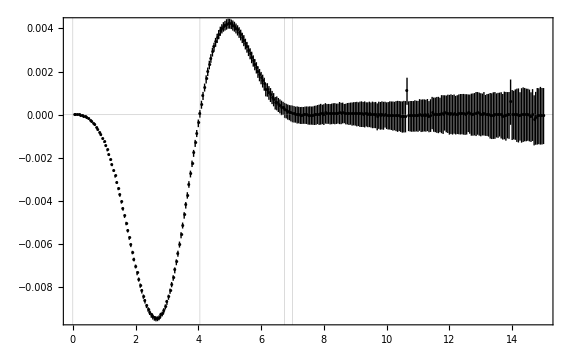

```mathematica
nexttoleadingorderbyshell=ErrorListPlot[Table[{resultsntl[[n,1]],ErrorBar[resultsntl[[n,2]]]},{n,1,Length[resultsntl]}],GridLines->{{0,4.05,6.75,7},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

The following gives the right-hand plot of Figure G1, showing density in space,

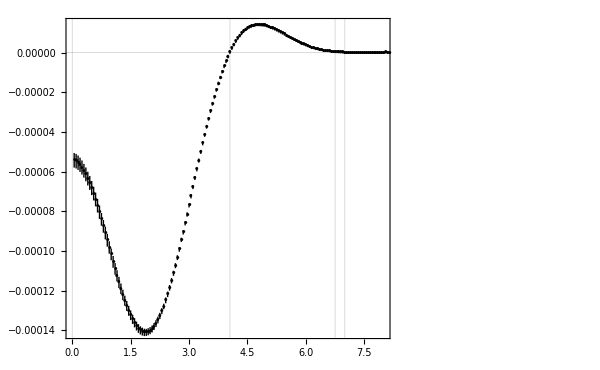

```mathematica
nexttoleadingorderdensity=ErrorListPlot[Table[{{resultsntl[[n,1,1]],resultsntl[[n,1,2]]/(4 π resultsntl[[n,1,1]]^2)},ErrorBar[resultsntl[[n,2]]/(4 π resultsntl[[n,1,1]]^2)]},{n,1,Length[resultsntl]}],GridLines->{{0,4.05,6.75,7},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->600,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,
FrameTicks->{{densityframeticks,Automatic},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

Now combine the two above plots to create Figure G1 in full,

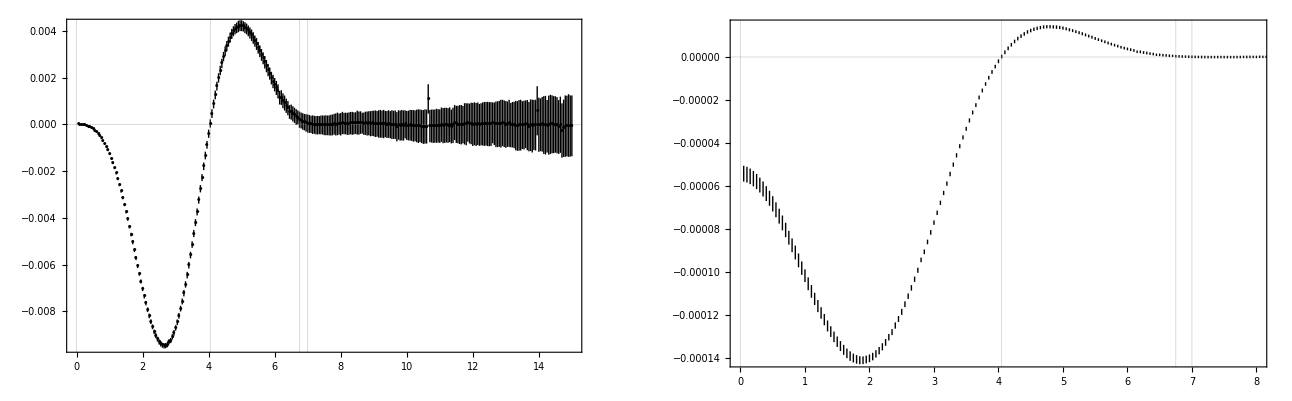

```mathematica
FigureG1=GraphicsRow[{nexttoleadingorderbyshell,nexttoleadingorderdensity},Alignment->Top]
```

If uncommented, the following exports Figure G1,

```mathematica
(* Export["EGCFigureG1.pdf",FigureG1]; *)
```

## Appendix G3: confirming the next-to-leading order distribution over space integrates to the total net entropy creation

Recall the total net entropy creation, calculated above for Appendix G1,

```mathematica
numericalintegration
```

-0.0115541

The next line sums all the values of the next-to-leading order entropy creation pattern function in the calculated range, and multiplies by 0.05000 to get an integrated value of the function, which is very close to the Appendix G1 result,

```mathematica
integratedntl=Sum[resultsntl[[n,1,2]],{n,1,Length[resultsntl]}] 0.05000
```

-0.0115463

The next line is similar, but only sums values out to r=7, and again is very close to the Appendix G1 result,

```mathematica
integratedntl7=Sum[resultsntl[[n,1,2]],{n,1,140}]×0.05000
```

-0.0114968

The next three lines implement the approach mentioned at the end of Appendix G3, integrating A_r' W_1(k_0 r') to get V_r' W_0(k_0 r'), and then doing the corresponding numerical integration, which yields the integrated next-to-leading order entropy creation pattern function, which we evaluate at r=15,

```mathematica
W0[z_]:=(3 (Sin[z]-z Cos[z]))/z^3
```

```mathematica
integraterW0[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0^2 k1^2 k2^2 r^3/3 W0[r k0] integratedoverv1expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

```mathematica
integraterW0[15]
```

{{15,-0.0115688},0.00192165,0.166105}

Although there is a relatively wide estimated error, the integration result again corresponds closely the Appendix G1 result

## Appendix G4

This part of the notebook follows that for Appendix F, adapted to the case where the perturbation has Maxwellian parameter σ1.

## Calculating the driving matrix (D̃)_1

From Eq. (E3), neglecting terms of higher order in V^-1, and leaving aside Maxwellian factors, we have

```mathematica
D1tilde0[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2 kp.v1)/(kp.kp) intf1[kp] V q[k2]+(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df10[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f10[kp,v2]+(ⅈ Subscript[k, J]^2 kp.v2)/(kp.kp) intf1[kp] V q[k1]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df10[kp,v2] (V q[k1]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f10[kp,v1]
```

```mathematica
D1tilde1[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df11[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f11[kp,v2]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df11[kp,v2] (V q[k1]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f11[kp,v1]
```

where D1tilde0 is associated with a Maxwellian with parameter σ, while D1tilde1 is associated with a Maxwellian with parameter σ1.  From Eq. (G14), we have, leaving aside the Maxwellian factor,

```mathematica
f10[p_,v_]:=-((ⅈ Subscript[k, J]^2 p.v (ω^2+p.p σ1^2+(3 σ1^4 (p.p)^2)/ω^2+(15 σ1^6 (p.p)^3)/ω^4))/(ω^2 p.p (ω^2+Subscript[k, J]^2 σ^2+(3 Subscript[k, J]^2 σ^4 (p.p))/ω^2+(15 Subscript[k, J]^2 σ^6 (p.p)^2)/ω^4))) (1+(p.v)/ω+((p.v)/ω)^2+((p.v)/ω)^3+((p.v)/ω)^4+((p.v)/ω)^5+((p.v)/ω)^6)
```

```mathematica
f11[p_,v_]:=ⅈ/ω (1+(p.v)/ω+((p.v)/ω)^2+((p.v)/ω)^3+((p.v)/ω)^4)
```

Note that use of p as the momentum variable is to avoid a variable k and the constant k_J getting confused by Mathematica. For the same reason k must not be used as a variable to which f1 is applied, although, for example k1 and k2, as in the definition of D1tilde do not cause any such problems.

Similarly, we have the integral of f1 with respect to v is

```mathematica
intf1[p_]:=ⅈ (1/ω+(σ1^2 p.p)/ω^3+(3 σ1^4 (p.p)^2)/ω^5)-(ⅈ (ω^2+σ1^2 p.p) (σ^2+(3 σ^4 p.p)/ω^2) Subscript[k, J]^2)/(ω^3 (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2))
```

and the derivative of f1 with respect to v is

```mathematica
df10[p_,v_]:=-(ⅈ (ω^2+σ1^2 p.p+(3 σ1^4 (p.p)^2)/ω^2) p.v (p/ω+(2 p p.v)/ω^2+(3 p (p.v)^2)/ω^3+(4 p (p.v)^3)/ω^4) Subscript[k, J]^2)/(ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))-(ⅈ p (ω^2+σ1^2 p.p+(3 σ1^4 (p.p)^2)/ω^2) (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3+(p.v)^4/ω^4) Subscript[k, J]^2)/(ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))+(ⅈ v (ω^2+σ1^2 p.p+(3 σ1^4 (p.p)^2)/ω^2) p.v (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3+(p.v)^4/ω^4) Subscript[k, J]^2)/(σ^2 ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2+(3 σ^4 p.p Subscript[k, J]^2)/ω^2+(15 σ^6 (p.p)^2 Subscript[k, J]^2)/ω^4))
```

```mathematica
df11[p_,v_]:=(ⅈ p (1/ω+(2 p.v)/ω^2+(3 (p.v)^2)/ω^3))/ω-(ⅈ v (1+(p.v)/ω+(p.v)^2/ω^2+(p.v)^3/ω^3))/(σ^2 ω)
```

## Calculating the variant of the vector ν (nu)

Eq. (F10) defines  the vector ν. Its first component is μ^(0) which is 0.  The second, fourth and sixth components are given by ν^(j)(k_1,k_2) for j=1,2,3.  The third, fifth and seventh are similarly ν^(j)(k_2,k_1).We write k_1 and k_2 in co-ordinate terms with their moduli k1 and k2, and the angle θ, which  k_2 makes to k_1; and we also now introduce the dummy variable κ.  Calculating the variant of ν allowing σ1≠σ takes less than two minutes on a standard PC:

```mathematica
G4ν=Join[{0},Flatten[Table[{term=(Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde0[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] F4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},σ^2 IdentityMatrix[4]]],{κ,0,3}]]+Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde1[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] F4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},σ1^2 IdentityMatrix[4]]],{κ,0,3}]]),term/.{k1->k2,k2->k1,θ->-θ}},{j,1,3}]]];
```

## Calculating the result, γ_a

The matrices M, L^-1 and Γ, and quantity smallγcoefficient have already been calculated above - they are independent of σ1 - so we can now write the variant (γ̃)_a, to second order in κ, as

```mathematica
G4γtilde=Series[smallγcoefficient Γcoefficients.LInverse.G4ν,{κ,0,2}];
```

To wrap up, we need to take the residue of this at (approximately) ω=ⅈη_1+ⅈη_2, which was calculated as ωres above, and we applying the residue theorem in the next line, keeping the result up to and including second order in κ.  This takes five to ten minutes on a standard PC.

```mathematica
G4γ=Series[Limit[-ⅈ*Simplify[G4γtilde(ω-ωres)],ω->ωres],{κ,0,2}];
```

We can put this into a more convenient form using the displayrule from above, which then gives us the final result for the variant of Eq. (F12) needed for Appendix G4, leaving aside the Maxwellian and exponential terms,

```mathematica
G4F12expression=Collect[G4γ//.displayrule,κ,Simplify]
```

(k1dotv1^2 σ1^2)/(4 k1^2 σ^4)-(k1dotv1^2 κ^2 (-8 k1dotkp^2 σ^4+6 k1dotkp kp^2 (σ^4+8 σ^2 σ1^2-4 σ1^4)+kp^2 (2 k1^2 (σ^4-33 σ^2 σ1^2+12 σ1^4)+3 σ1^2 (2 k1dotv1^2+kp^2 (-9 σ^2+5 σ1^2)))))/(24 k1^2 kp^2 σ^6 k_J^2)-(ⅈ k1dotv1 κ (-8 k1dotkp^2 σ^4+6 k1dotkp kp^2 (σ^4+8 σ^2 σ1^2-4 σ1^4)+kp^2 (k1^2 (2 σ^4-57 σ^2 σ1^2+24 σ1^4)+3 σ1^2 (2 k1dotv1^2+kp^2 (-9 σ^2+5 σ1^2)))))/(24 k1^2 kp^2 σ^5 k_J)+(ⅈ k1dotv1 σ1^2 k_J)/(4 k1^2 κ σ^3)

For the σ1=σ case, from above, we have

```mathematica
E29orF12expression
```

k1dotv1^2/(4 k1^2 σ^2)+κ^2 (-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4))/(12 k1^2 kp^2 σ^2 k_J^2))+κ (-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4))/(24 k1^2 kp^2 σ k_J))+(ⅈ k1dotv1 k_J)/(4 k1^2 κ σ)

The following confirms that our E12expression is the same as this, when σ1 is set to σ,

```mathematica
Simplify[((G4F12expression)/.{σ1->σ})-E29orF12expression]
```

0

## Preparing and doing the numerical integration

We now, as explained just before Eq. (G2), need to swap k_1↔-k_+ in the above expression,

```mathematica
G4G2expression=G4F12expression/.{k1dotv1->-kpdotv1,k1->-kp,kp->-k1};
```

The derivative-related expression in Eq. (G3) is, leaving aside the terms of order k_1^3 and higher, and also leaving aside the exponential factors.  Here we have written k1vect to represent the vector quantity k_1, and it will be manipulated appropriately below.  As for its scalar cousins, it attracts a factor of κ,

```mathematica
η=Subscript[k, J] σ-(3 σ (κ k1)^2)/(2 Subscript[k, J])+(15 σ (κ k1)^4)/(8 Subscript[k, J]^3);
```

```mathematica
Y1=-(1/(ⅈ η)+(σ1^2 (κ k1)^2)/(ⅈ η)^3 +(3 σ1^4 (κ k1)^4)/(ⅈ η)^5+(15 σ1^6 (κ k1)^6)/(ⅈ η)^7);
```

```mathematica
G4G3expression=Collect[Normal[Series[-(ⅈ Subscript[k, J]^2 σ^2 κ k1vect V η Y1)/((κ k1dotv1-ⅈ η)(σ^2(Subscript[k, J]^2-(κ k1)^2)-η^2))(1-(κ k1dotv1)/(κ k1dotv1-ⅈ η)),{κ,0,2}]],κ,Simplify];
```

To get the variant integrand of Eq. (G1) (still leaving aside the exponential factors, which we assume to be constant over the integration), we need to multiply G4G2expression with the dot product of k_2/(κ k_2^2)and G4G3expression,

```mathematica
G4G1integrand=G4G2expression G4G3expression/k1vect k1dotk2/(κ k2^2);
```

In the next two lines, we now integrate this with respect to v_1, to get the result set out in Eq. (F4).  To do this, we define vx to be the component of v_1 parallel to k_1, and vy to be the other component of v_1 which lies in the plane made by k_1 and k_2 (or an arbitrary direction perpendicular to k_1, if k_1 and k_2 are co-linear).  We also write cth for the cosine of the angle θ between k_1 and k_2. Then we can write

```mathematica
G4G1integranda=Simplify[G4G1integrand/.{k1dotv1->k1 vx,kpdotv1->k1 vx+k2(cth vx + √(1-cth^2) vy)}];
```

where the term within round brackets is k2dotv1.  We now do the v_1 integration, using Gaussian moments, via the appropriate Mathematica function, to get

```mathematica
G4G4expression=Collect[Series[Expectation[G4G1integranda,{vx,vy}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]],{κ,0,0}],{V,κ},Simplify];
```

As an aside, we can also write this in a nicer form corresponding to that displayed in Eq. (G4),

```mathematica
G4G4expressiondisplay=Collect[Normal[Series[G4G4expression/.{cth->k1dotk2/(k1 k2)},{κ,0,0}]],{V,κ,σ1},Simplify]
```

V ((ⅈ k1dotk2 (k1^2-k2^2) (-4 k1dotkp^2+k1^2 (3 k1dotkp+kp^2)))/(24 k1^4 k2^2 kp^2 σ k_J)-(ⅈ k1dotk2 (6 k1^4+6 k1dotk2^2+k2^2 (8 k1dotkp+3 k2^2-11 kp^2)+k1dotk2 (6 k2^2-3 kp^2)+k1^2 (3 k1dotk2-8 k1dotkp-6 k2^2+8 kp^2)) σ1^2)/(8 k1^2 k2^2 kp^2 σ^3 k_J)+(ⅈ k1dotk2 (k1^2-k2^2) (7 k1^2-8 k1dotkp+8 kp^2) σ1^4)/(16 k1^2 k2^2 kp^2 σ^5 k_J)-(ⅈ k1dotk2 (k1^2-k2^2) σ1^2 k_J)/(8 k1^2 k2^2 kp^2 κ^2 σ^3))

The corresponding expression from the notebook for Appendix G1-3, with σ1=σ, is

```mathematica
G4expressiondisplay
```

V (-(ⅈ k1dotk2 (15 k1^6-8 k1dotkp^2 k2^2+k1^4 (18 k1dotk2-30 k1dotkp-15 k2^2+22 kp^2)+2 k1^2 (18 k1dotk2^2+4 k1dotkp^2+18 k1dotk2 k2^2+15 k1dotkp k2^2+9 k2^4-9 k1dotk2 kp^2-20 k2^2 kp^2)))/(48 k1^4 k2^2 kp^2 σ k_J)-(ⅈ k1dotk2 (k1^2-k2^2) k_J)/(8 k1^2 k2^2 kp^2 κ^2 σ))

The following confirms that the new expression, with σ1 set to σ is the same as the old expression,

```mathematica
Simplify[Collect[G4G4expressiondisplay/.σ1->σ,κ,Simplify]-G4expressiondisplay]
```

0

Our G4G4expression can be split into an order -2 expression

```mathematica
G4G4expressionorderm2=Collect[SeriesCoefficient[G4G4expression,{κ,0,-2}],{V,κ},Simplify]
```

-(ⅈ k1dotk2 (k1^2-k2^2) V σ1^2 k_J)/(8 k1^2 k2^2 kp^2 σ^3)

which, as for the σ1=σ case vanishes on integration by k_1 and k_2.  The above expression is (σ1/σ)^2 times the expression for σ1=σ, which from above was

```mathematica
G4expressionorderm2
```

-(ⅈ k1dotk2 (k1^2-k2^2) V k_J)/(8 k1^2 k2^2 kp^2 σ)

implying that at leading order the entropy-creation pattern function is the same as for the σ1=σ .

We also have an order 0 expression,

```mathematica
G4G4expressionorder0=Collect[SeriesCoefficient[G4G4expression,{κ,0,0}],{V,κ},Simplify];
```

This is as far as we can go analytically, so we now take out the constants V and k_J from the expression, put k_+ in terms of k_1, k_2 and cth, and then integrate numerically, multiplying by -ⅈ so the result is the constant factor after the first equality in  Eq. (57).  We also multiply by σ^5 as opposed to σ in the notebook for Appendix F1-3,

```mathematica
G4G4expressionorder0fornumerical=Simplify[(G4G4expressionorder0 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})(σ^5 Subscript[k, J])/V]
```

-(ⅈ cth (8 cth^2 k2^2 (k1^2-k2^2) σ^4+3 k1^4 (12 σ^2 σ1^2-7 σ1^4)+6 cth k1^3 k2 (σ^4+8 σ^2 σ1^2-4 σ1^4)-6 cth k1 k2^3 (σ^4+11 σ^2 σ1^2-4 σ1^4)-k1^2 k2^2 (2 σ^4+6 σ^2 σ1^2+3 σ1^4)+2 k2^4 (σ^4-24 σ^2 σ1^2+12 σ1^4)))/(48 k1 k2 (k1^2+2 cth k1 k2+k2^2))

From the above, we can see that the expression contains various combinations of σ1 and σ.  We therefore form a CoefficientList before doing the numerical integration,

```mathematica
G4G4expressionorder0fornumericallist=CoefficientList[G4G4expressionorder0fornumerical,{σ,σ1}];
```

We now doing the numerical integrations, keeping track of estimated errors, and dividing by σ^4 to maintain compatibility with the result of the notebook for Appendix F1-3,

```mathematica
G4errorsG1=ConstantArray[Null,{5,5}];G4numericalintegration=Expand[1/σ^4 Chop[Sum[σ^n σ1^n1 (-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 G4G4expressionorder0fornumericallist[[n+1,n1+1]]),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((G4errorsG1[[n+1,n1+1]]=Through[#1@"Error"])&)]),{n,0,4},{n1,0,4}]]]
```

-0.00178767-(0.0113885 σ1^2)/σ^2+(0.00162298 σ1^4)/σ^4

We check that, in the σ1=σ case, this gives essentially the same answer as in the Appendix F1-3 notebook

```mathematica
ScientificForm[(((G4numericalintegration)/.{σ1->σ})-numericalintegration)/numericalintegration]
```

-8.41328×10^-5

which it does.

The estimated errors of our numerical integrations are, in the order of ascending powers of σ1,

```mathematica
{Total[G4errorsG1[[4+1,0+1]]],Total[G4errorsG1[[2+1,2+1]]],Total[G4errorsG1[[0+1,4+1]]]}
```

{9.90667×10^-6,9.98768×10^-6,9.96555×10^-6}

With thanks to Anton Antonov for his very useful post at https://mathematica.stackexchange.com/questions/26401/determining-which-rule-nintegrate-selects-automatically/96663#96663 for explaining how to extract error estimates from NIntegrate (see the table in the post’s “Update 2”), and also to MichaelE2 for his helpful post at https://mathematica.stackexchange.com/questions/75426/obtaining-an-nintegrate-error-estimate

We can see that there is negative net entropy creation, unless x≡σ1/σ is sufficiently large,

```mathematica
Reduce[(G4numericalintegration/.{σ1->x,σ->1})>0&&x>0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>2.6778

This is only more pronounced than the average size of the entropy destruction in the core and creation in the halo if y=x β is sufficiently large (assuming only the final term of numericalintegration is then non-negligible),

```mathematica
Reduce[0.0016229806640536632 y^2>(0.01104398794177712+0.011019599846490175)/2&&y>0,y]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

y>2.60715

## Calculating next-to-leading order distribution over space plots for the limit σ1→0, and plotting Figure G2

This part of the notebook is along the lines of the similar part of the Appendix F1-3 notebook.

From Eq. (G8), we see that, for calculating the distribution over space, we need to modify F3expression from above, change occurrences of k_1 to k_01,

```mathematica
G4G3expression01=G4G3expression/.{k1->k01,k1dotv1->k01dotv1,k1vect->k01vect};
```

Then putting G4G3expression01 in the form

```mathematica
G4G3expression01a=G4G3expression01/.{k01->√(k01v.k01v),k01dotv1->k01v.v1v};
```

Now for G4G2expression, found above, the corresponding form is

```mathematica
G4G2expressiona=Simplify[G4G2expression/.{kpdotv1->k12v.v1v,kp->√(k12v.k12v),k1->√(k1v.k1v),k1dotkp->k1v.k12v}];
```

Now combine G4G2expressiona and G2G3expression01a to get the integrand of Eq. (G8), other than the window function and the (2π)^-3 factors, set σ1=0, and pick out the terms of order 0 in κ,

```mathematica
integrandexpression=Simplify[SeriesCoefficient[((G4G2expressiona G4G3expression01a/k01vect (k01v.k2v)/(κ k2v.k2v))/.σ1->0),{κ,0,0}]]
```

-(ⅈ (3 cth k1-k2+4 cth^2 k2) V (k1 vx+cth k2 vx+√(1-cth^2) k2 vy) (cth (cpsi k0+k1)+√((-1+cpsi^2) (-1+cth^2)) k0 Cos[ϕ]) (2 cpsi k0 vx+k1 vx-cth k2 vx-√(1-cth^2) k2 vy+2 √(1-cpsi^2) k0 vy Cos[ϕ]+2 √(1-cpsi^2) k0 vz Sin[ϕ]))/(24 (k0^2+2 cpsi k0 k1+k1^2) (k1^2+2 cth k1 k2+k2^2) σ^3 k_J)

We now do the integration with respect to v_1, using Gaussian moments, via the appropriate Mathematica function, and extract non-numerical constants,

```mathematica
integratedoverv1expression=Simplify[ (σ Subscript[k, J])/V Expectation[integrandexpression,v1v\[Distributed]MultinormalDistribution[{0,0,0},σ^2 IdentityMatrix[3]]]]
```

-(ⅈ (3 cth k1-k2+4 cth^2 k2) (cth (cpsi k0+k1)+√((-1+cpsi^2) (-1+cth^2)) k0 Cos[ϕ]) (k1^2-k2^2+2 cpsi k0 (k1+cth k2)+2 √((-1+cpsi^2) (-1+cth^2)) k0 k2 Cos[ϕ]))/(24 (k0^2+2 cpsi k0 k1+k1^2) (k1^2+2 cth k1 k2+k2^2))

The following function then does the required numerical integration, for next-to-leading order,

```mathematica
integraterntl[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] integratedoverv1expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning - as for its leading order equivalent, integrater - a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Again, as for its the corresponding leading order function, integrater, without Quiet, this function will typically give rise to (non-fatal) error messages, so keeping track of error estimates is important.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000...15.00000 from the data file,

```mathematica
G4resultsntl=<<" Patterns Wren 2018 data.m"[[4]];
```

Alternatively, the results can be calculated (and exported) using the following code, when uncommented.  This takes about three to five hours on a standard PC:

```mathematica
(*( G4resultsntl={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,G4resultsntl=Join[G4resultsntl,{integraterntl[r]}]]
,G4resultsntl//MatrixForm//ScientificForm];Export["Appendix G4 Variant data.m",G4resultsntl];G4resultsntl//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure G2, showing the stationary entropy-creation pattern function by shell,

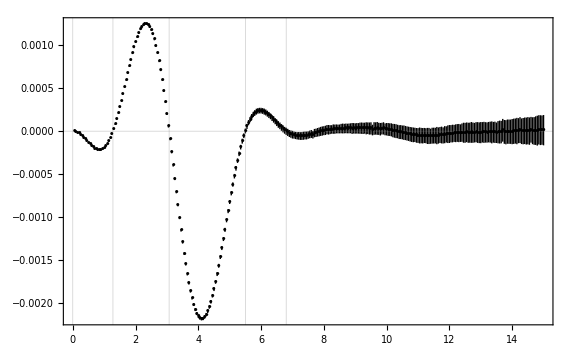

```mathematica
nexttoleadingorderbyshell=ErrorListPlot[Table[{G4resultsntl[[n,1]],ErrorBar[G4resultsntl[[n,2]]]},{n,1,Length[G4resultsntl]}],GridLines->{{0,1.28,3.07,5.5,6.8},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{\\,stat}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

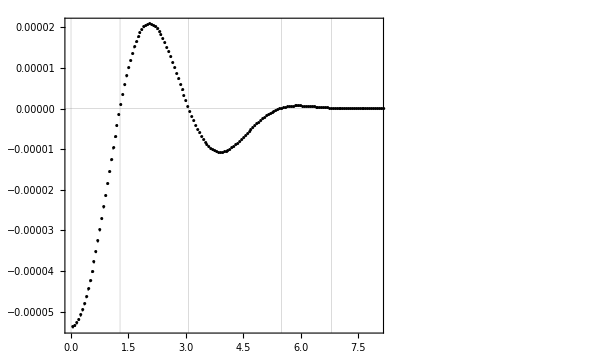

```mathematica
nexttoleadingorderdensity=ErrorListPlot[Table[{{G4resultsntl[[n,1,1]],G4resultsntl[[n,1,2]]/(4 π G4resultsntl[[n,1,1]]^2)},ErrorBar[G4resultsntl[[n,2]]/(4 π G4resultsntl[[n,1,1]]^2)]},{n,1,Length[G4resultsntl]}],GridLines->{{0,1.28,3.07,5.5,6.8},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->590,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^{\\circ\\text{\\,stat}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,
FrameTicks->{{densityframeticks,Automatic},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

Now combine the two above plots to create Figure G2 in full,

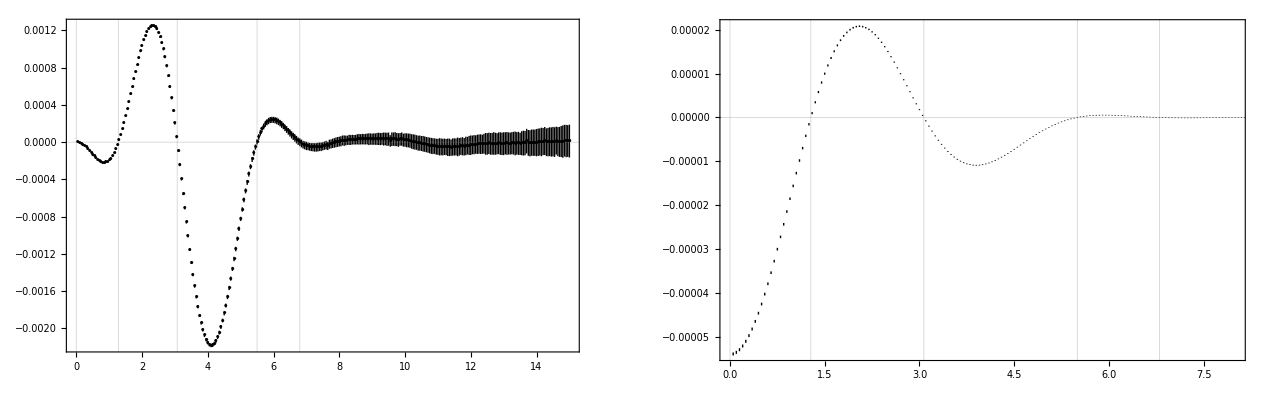

```mathematica
FigureG2=GraphicsRow[{nexttoleadingorderbyshell,nexttoleadingorderdensity},Alignment->Top]
```

If uncommented, the following exports Figure G2,

```mathematica
(*Export["EGCFigureG2.pdf",FigureG2]; *)
```

If uncommented, and if the relevant datasets have been calculated above, the following produces the data file “ Patterns Wren 2018 data.m”.

```mathematica
(*Export[" Patterns Wren 2018 data.m",{B3data,results,resultsntl,G4resultsntl}]*)
```

#### End of main notebook

## The remainder of the notebook contains initialisation cells that are automatically evaluated first. They are used for formatting Figures, and for scientific form numbers

For formatting Figures

Define theme and colours:

```mathematica
$PlotTheme="Scientific";
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

Define the formats for the plot lines:

```mathematica
ps8log={{colors[[1]],Dotted},{colors[[2]],Dashing[{0.005,0.005}]},{colors[[3]],Dashing[{0.01,0.01}]},{colors[[4]],Dashing[{0.02,0.02}]}};
```

```mathematica
ps8=Join[{Black},ps8log];
```

Set up the MaTeX package

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xfrac}","\\usepackage[T1]{fontenc}"}];
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};DefaultBaseStyle->texStyle;
```

Define the frame ticks for Figure B1 (Right):

```mathematica
laxsticks={{{{1-1*10^-2,MaTeX["-10^{-2}+1"]},{1-1*10^-3,MaTeX["-10^{-3}+1"]},(*{1-5*10^-4,MaTeX["-5\\!\\times \\!10^{-4}+1"]},{1-1*10^-4,MaTeX["-10^{-4}+1"]},*){1,1},(*{1+1*10^-4,MaTeX["10^{-4}+1"]},*){1+1*10^-3,MaTeX["10^{-3}+1"]},{1+1*10^-2,MaTeX["10^{-2}+1"]}},None},{Automatic,None}};
```

Define the legend for Figure B1:

```mathematica
magn=1.5;pl={MaTeX["\\text{Numerical solution}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\frac{3\\sigma k^2}{2 k_\\text{J}}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{15\\sigma k^4}{8 k_\\text{J}^3}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots-\\frac{147\\sigma k^6}{16 k_\\text{J}^5}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{9531\\sigma k^8}{128 k_\\text{J}^7}",Magnification->magn]};
```

The following defines frame ticks for the right-hand plots of Figures 2, G1 and G2:

```mathematica
densityframeticks={{-1/10000,"-10 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-1/20000,"-5 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-3/10000,"-15 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{3/100000,"",{0.005,0}},{1/50000,"",{0.005,0}},{1/100000,"",{0.005,0}},{0,"",{0.005,0}},{-1/100000,"",{0.005,0}},{-1/50000,"",{0.005,0}},{0,"0"},{-3/100000,"",{0.005,0}},{-1/25000,"",{0.005,0}},{-1/20000,"",{0.005,0}},{-3/50000,"",{0.005,0}},{-7/100000,"",{0.005,0}},{-1/12500,"",{0.005,0}},{-9/100000,"",{0.005,0}},{-1/10000,"",{0.005,0}},{-11/100000,"",{0.005,0}},{-3/25000,"",{0.005,0}},{-13/100000,"",{0.005,0}},{-7/50000,"",{0.005,0}},{-3/20000,"",{0.005,0}}};
```

Load the ErrorBarPlots package for Figures 2, F1 and F2:

```mathematica
Needs["ErrorBarPlots`"]
```

Define a function to give scientific form numbers, with proper padding by zeros to the right of the decimal - with thanks to N.J. Evans at https://mathematica.stackexchange.com/questions/96832/scientific-form-with-padding-and-exponent :

```mathematica
paddedscientificform[x_,n_]:=PaddedForm[x,{n,n-1},ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row@{#1,"×",Superscript["10",ToString[#3]]}&)]
```